```mathematica
erf =({LightGray,Arrowheads[{0,.015}],Arrow[#1,.35]}&);
```

```mathematica
vcr1={{0,0(*Search*)},{2,2 (*Customers*)},{2,1 (*Stock*)},{2,-1(*Orders*)},{2,-2 (*Supplies*)}, {5,2 (*MasterDetail*)}};
vrf = ({White, EdgeForm[Blue],Black,
Inset[Style[#2, FontSize -> 14, FontFamily -> "Cambria" ], #1]}&);
```

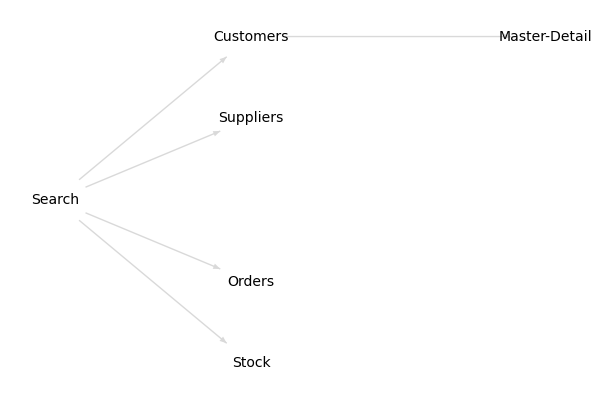

```mathematica
gpSeach=GraphPlot[{search -> customers,search ->  suppliers, search -> orders, search -> stock, customers->masterDetail }, VertexLabeling -> True, DirectedEdges-> True,VertexLabeling -> True, DirectedEdges-> True,EdgeRenderingFunction->erf,VertexCoordinateRules->vcr1,MultiedgeStyle->1,VertexRenderingFunction-> vrf, ImageSize ->{600, 400}]
```

```mathematica
search=Framed[ Style["Search", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Search

```mathematica
customers=Framed[ Style["Customers", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Customers

```mathematica
suppliers=Framed[ Style["Suppliers", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Suppliers

```mathematica
orders=Framed[ Style["Orders", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Orders

```mathematica
stock=Framed[ Style["Stock", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Stock

```mathematica
masterDetail=Framed[ Style["Master-Detail", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Master-Detail

```mathematica
addNew=Framed[ Style["Add New", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Add New

```mathematica
details=Framed[ Style["Details", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Details

```mathematica
ordersMasterDetail=Framed[ Style["Orders (Master-Detail)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Orders (Master-Detail)

```mathematica
vrf = ({White, EdgeForm[Blue],Black,
Inset[Style[#2, FontSize -> 14, FontFamily -> "Cambria" ], #1]}&);
```

```mathematica
vcr2={{0,0(*Customers*)},{3,2 (*Add New*)},{3,0 (*Details*)},{3,-2  (*(Orders master detail*)}}
```

{{0,0},{3,2},{3,0},{3,-2}}

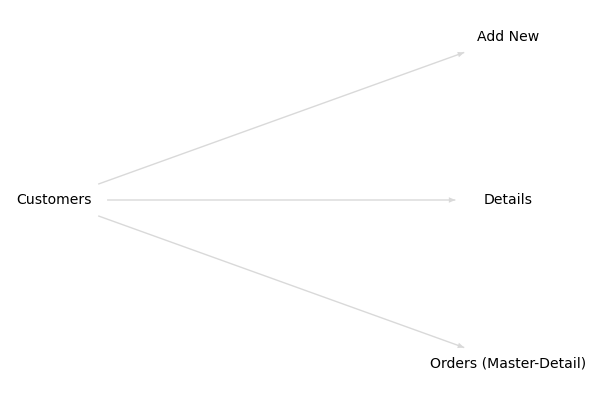

```mathematica
gpCustomers=GraphPlot[{ customers -> addNew, customers -> details, customers -> ordersMasterDetail}, VertexLabeling -> True, DirectedEdges-> True,VertexLabeling -> True, DirectedEdges-> True,EdgeRenderingFunction->erf,VertexCoordinateRules->vcr2,MultiedgeStyle->1,VertexRenderingFunction-> vrf, ImageSize ->{600, 400}]
```

```mathematica
suppliers
```

Suppliers

```mathematica
stock
```

Stock

```mathematica
adminDAL=Framed[ Style["Admin (DAL)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Admin (DAL)

```mathematica
xmlStock =Framed[ Style["XML", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

XML

```mathematica
generate=Framed[ Style["Generate", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Generate

```mathematica
viewFormatted=Framed[ Style["View Formatted", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

View Formatted

```mathematica
edit=Framed[ Style["Edit", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Edit

```mathematica
currentStockXML=Framed[ Style["CurrentStock.xml", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

CurrentStock.xml

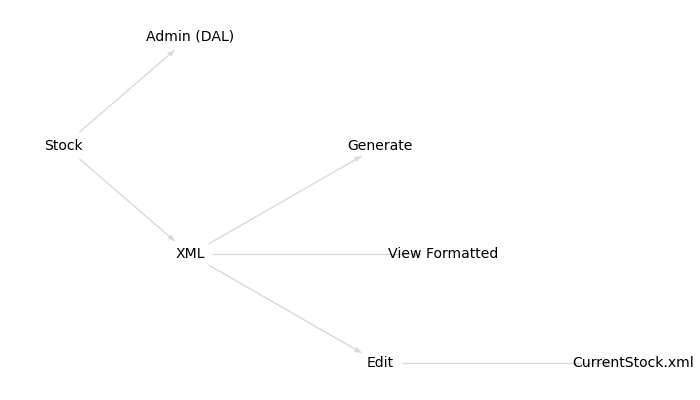

```mathematica
vcr3={{0,0(*stock*)},{2,2 (*adminDAl*)},{2,-2(*XML*)},{5,0  (*(generate*)},{6,-2  (*(viewFormatted*)},{5,-4 (*(edit*)},{9,-4  (*(currenStockXML*)}};
gpStock=GraphPlot[{ stock -> adminDAL, stock -> xmlStock, xmlStock -> generate, xmlStock -> viewFormatted, xmlStock -> edit, edit -> currentStockXML}, VertexLabeling -> True, DirectedEdges-> True,VertexLabeling -> True, DirectedEdges-> True,EdgeRenderingFunction->erf,VertexCoordinateRules->vcr3,MultiedgeStyle->1,VertexRenderingFunction-> vrf, ImageSize ->{700, 400}]
```

```mathematica
supplerdetails=Framed[ Style["Details (ADO.net)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Details (ADO.net)

```mathematica
suppleradmin=Framed[ Style["Admin (DAL)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Admin (DAL)

```mathematica
newSupplierXML =  Framed[ Style["New Supplier (XML)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

New Supplier (XML)

```mathematica
edit
```

Edit

```mathematica
create =  Framed[ Style["Create", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Create

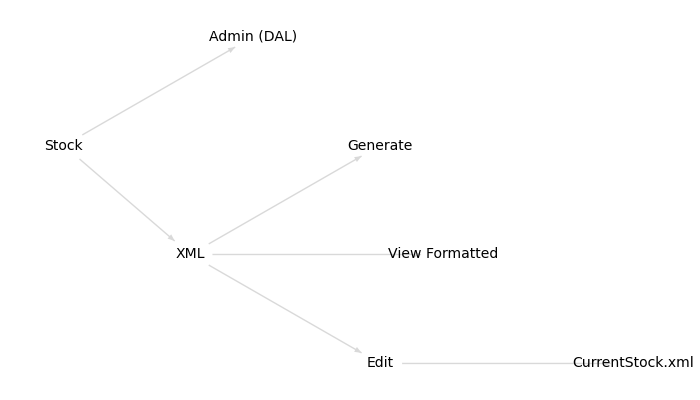

```mathematica
vcr4={{0,0(*stock*)},{3,2 (*adminDAl*)},{2,-2(*XML*)},{5,0  (*(generate*)},{6,-2  (*(viewFormatted*)},{5,-4 (*(edit*)},{9,-4  (*(currenStockXML*)}};
gpSupp=GraphPlot[{ stock -> adminDAL, stock -> xmlStock, xmlStock -> generate, xmlStock -> viewFormatted, xmlStock -> edit, edit -> currentStockXML}, VertexLabeling -> True, DirectedEdges-> True,VertexLabeling -> True, DirectedEdges-> True,EdgeRenderingFunction->erf,VertexCoordinateRules->vcr4,MultiedgeStyle->1,VertexRenderingFunction-> vrf, ImageSize ->{700, 400}]
```